```mathematica
LibraryUnload[libhello]
```

```mathematica
<<"/Users/ckorikov/_syntacore/projects/wolfram_russianhack18_scr1/cpp_bridge/math.m"
```

```mathematica
pclist = Table[nextpc[],10000];
```

```mathematica
g=BlockMap[#[[1]]->#[[2]]&,pclist,2,1];
```

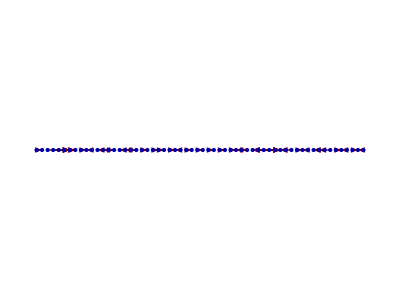

```mathematica
GraphPlot[Select[g,(#[[2]]-#[[1]])>100&],DirectedEdges-> True,Method->"LinearEmbedding"]
```

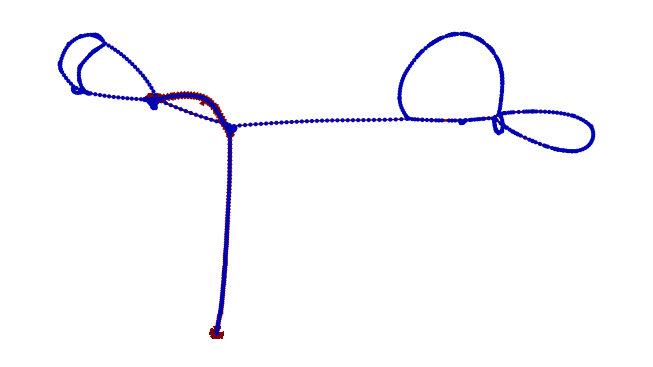

```mathematica
GraphPlot[g[[2000;;9000]],DirectedEdges-> True]
```

```mathematica
Dataset[Table[{i,BaseForm[getregister[i],16],BaseForm[getregister[i],2]},{i,1,31}]]
```

Dataset[<>]